λ^2/(1-λ^2)

```mathematica
Simplify[(1-λ^2)^2 Sum[(λ^(n+m)) Factorial[n]*Factorial[m],{n,0,∞},{m,0,∞}]]
```

(-1+λ^2)^2 ∑_(n=0)^∞ ∑_(m=0)^∞ λ^(m+n) m! n!

```mathematica
p1=Simplify[(1-λ^2)^2 Sum[(λ^(n+1)) ,{n,0,∞}]^2]
```

λ^2 (1+λ)^2

```mathematica
p2=Simplify[(1-λ^2)^2 Sum[(λ^(n+2)) ,{n,0,∞}]^2]
```

λ^4 (1+λ)^2

```mathematica
px=Simplify[(1-λ^2)^2 Sum[(λ^(n+x)) ,{n,0,∞}]^2]
```

λ^(2 x) (1+λ)^2

```mathematica
(2p2)/(p1+2p2)^2
```

```mathematica
g2simple=(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)
```

(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)

```mathematica
g2simple/.{λ->0.01}
```

1.95981

```mathematica
{λ^2/(1-λ^2),g2simple}/.{λ->Abs[lambdaGivenN[0.0001]]}
```

{0.0001,1.95981}

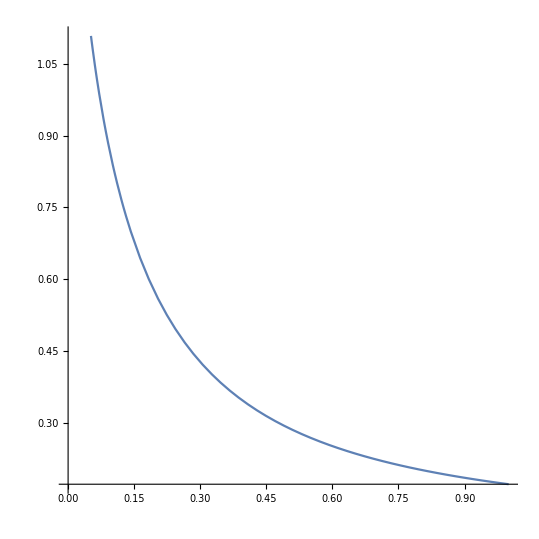

```mathematica
Plot[g2simple/.{λ->Abs[lambdaGivenN[x]]},{x,1,10^-4},AspectRatio->1]
```

```mathematica
g2full=Sum[n(n-1)(px/.{x->n}),{n,0,∞}]/Sum[n(px/.{x->n}),{n,0,∞}]^2
```

-(2 (-1+λ))/(1+λ)

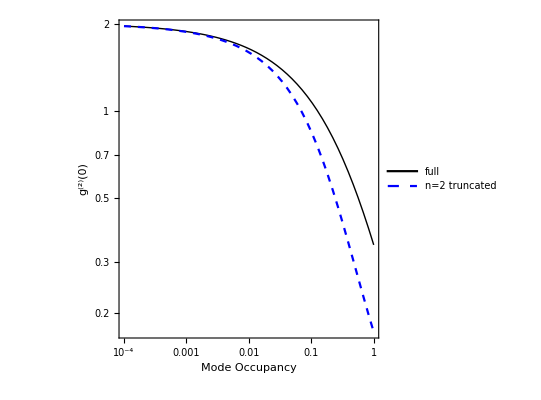

```mathematica
LogLogPlot[{g2full/.{λ->Abs[lambdaGivenN[x]]},g2simple/.{λ->Abs[lambdaGivenN[x]]}},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"full","n=2 truncated"},Center],PlotStyle->{{Black,Thick},{Blue,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","g^(2)(0)"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

```mathematica
SameQ[FullSimplify[-(2 (-1+λ))/(1+λ)],FullSimplify[(2 (1-λ))/(1+λ)]]
```

True

```mathematica
lambdaGivenN=InverseFunction[(#)^2/(1-(#)^2)&]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-(√#1)/(√(1+#1))&

```mathematica
a=Abs[]
λ^2/(1-λ^2)/.λ->a
```

0.031607

0.001

```mathematica
λ^2/(1-λ^2)/.{λ->0.02}
```

0.00040016

```mathematica
Limit[(2p2)/(p1+2p2)^2,λ->0]
```

2

```mathematica
Simplify[ Sum[(√(λ^n Factorial[n])√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞},{m,0,∞}]]
```

∑_(n=0)^∞ ∑_(m=0)^∞ (λ^n (λ/(1+λ))^n n!)/(1+λ)

```mathematica
p1=Simplify[ Sum[(√(1/(λ+1)(λ/(λ+1))^1)√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞}]]
```

λ/(1+λ)^2

```mathematica
p2=Simplify[ Sum[(√(1/(λ+1)(λ/(λ+1))^2)√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞}]]
```

λ^2/(1+λ)^3

```mathematica
p2/p1^2
```

1+λ

```mathematica
Factorial[X-N]
```

(-N+X)!

```mathematica
FullSimplify[1/(Factorial[m]Factorial[n])Factorial[m+n],Assumptions->{n>0,m>0}]
```

((m+n)!)/(m! n!)

```mathematica
Factorial[0]
```

1

```mathematica
Sum[Factorial[X]/(Factorial[m]Factorial[X-m]),{m,0,∞}]
```

2^X

```mathematica
NSum[1/Factorial[m],{m,0,∞}]
```

2.71828

```mathematica
Expand[((1-L^2)L^x)^2]
```

L^(2 x)-2 L^(2+2 x)+L^(4+2 x)

```mathematica
Expand[((1-L^2))^2]
```

1-2 L^2+L^4

```mathematica
Expand[2 ( ( 1-λ^2) λ^X)^2]
```

2 λ^(2 X)-4 λ^(2+2 X)+2 λ^(4+2 X)

```mathematica
Expand[(1-2 λ^2+λ^4)(2 λ^(2X))]
```

2 λ^(2 X)-4 λ^(2+2 X)+2 λ^(4+2 X)

```mathematica
SameQ[FullSimplify[2 ( ( 1-λ^2) λ^X)^2],FullSimplify[2(1-2 λ^2+λ^4)(λ^(2X))]]
```

True

```mathematica
Sum[λ^(x 2),{x,1,∞}]
```

-λ^2/(-1+λ^2)

```mathematica
Sum[2 ( ( 1-λ^2) λ^X)^2{x,1,∞},Assumptions->λ<1,λ>0]
```

Sum::vloc: The variable Assumptions→λ<1 cannot be localized so that it can be assigned to numerical values.

Sum[2 ((1-λ^2) λ^X)^2 {x,1,∞},Assumptions→λ<1,λ>0]

```mathematica
Simplify[2(1-2 λ^2+λ^4)(-λ^2/(-1+λ^2))+(1-λ^2)^2]
```

1-λ^4

```mathematica
ncoProb=1-λ^4
noProb=(1-λ^2)^2
noProb/.λ->0.5
```

1-λ^4

(1-λ^2)^2

0.5625

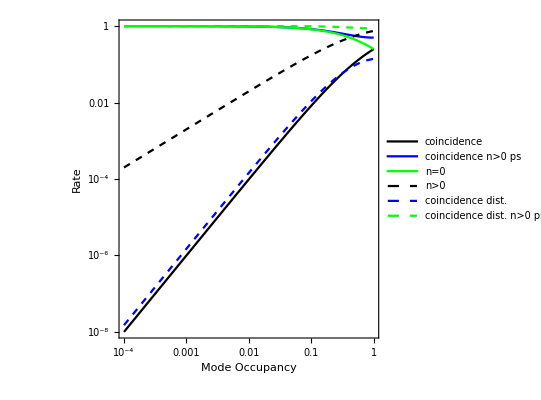

```mathematica
LogLogPlot[{1-ncoProb/.{λ->Abs[lambdaGivenN[x]]},
1-(ncoProb-noProb)/.{λ->Abs[lambdaGivenN[x]]},
noProb/.{λ->Abs[lambdaGivenN[x]]},
1-noProb/.{λ->Abs[lambdaGivenN[x]]},
ncoSomeCountsDistProb/.{λ->Abs[lambdaGivenN[x]]},
1-ncoSomeCountsDistProb/.{λ->Abs[lambdaGivenN[x]]}
},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue},{Green},{Black,Dashed},{Blue,Dashed},{Green,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

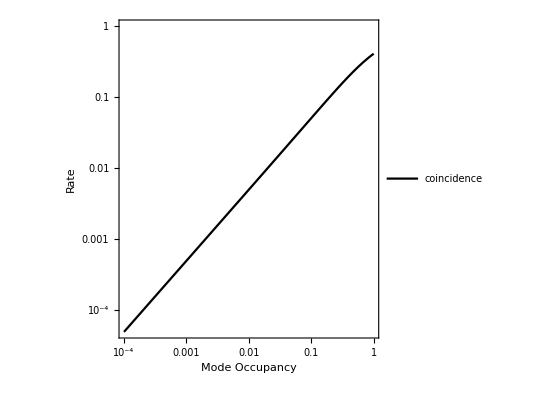

```mathematica
LogLogPlot[{(1-ncoProb/.{λ->Abs[lambdaGivenN[x]]})/(1-ncoDistProb)/.{λ->Abs[lambdaGivenN[x]]}},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","0 counts",">0 counts","no coincidence dist.","no coincidence counts >0 dist."},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

```mathematica
Series[x^y,{x,0}]
```

Series::sspec: Series specification {x,0} is not a list with three elements.

```mathematica
Series[x^y,{y,0,3}]
```

1+Log[x] y+1/2 Log[x]^2 y^2+1/6 Log[x]^3 y^3+O[y]^4

```mathematica
FullSimplify[(Sum[(1-λ^2)(λ^nTot)^2 1,{nTot,0,∞},{p,0,nTot+1}])^2]
```

((-2+λ^2)^2)/((-1+λ^2)^2)

```mathematica
ncoSomeCountsDistProb=FullSimplify[Sum[(1-λ^2)^2(λ^nTot)^2 2 (1/2)^nTot,{nTot,2,∞},{p,0,nTot}]]
ncoSomeCountsDistProb/.λ->0.5
```

-(2 λ^4 (-3+λ^2) (-1+λ^2)^2)/((-2+λ^2)^2)

0.0631378

```mathematica
ncoDistProb=ncoSomeCountsDistProb+noProb
ncoDistProb/.λ->0.5
```

(1-λ^2)^2-(2 λ^4 (-3+λ^2) (-1+λ^2)^2)/((-2+λ^2)^2)

0.625638

```mathematica
FullSimplify[(1-λ^2)^2 Sum[(λ^n)^2 (n+1)2 (1/2)^n,{n,0,∞}]-(1-λ^2)^2]
```

(-1+λ^2)^2 (-1+8/((-2+λ^2)^2))

```mathematica
noDistProb=(1-λ^2)^2
```

(1-λ^2)^2

```mathematica
ncoDistProb/.λ->0.1
```

1.20331